## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.2; qscal=0.25; Q=0.99;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.244264-4.07262×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.173522

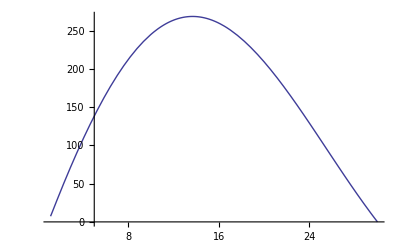

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-9.07142×10^-9},{30.2,-8.57371×10^-9},{30.4,-8.1034×10^-9},{30.6,-7.66181×10^-9},{30.8,-7.24729×10^-9},{31.,-6.85657×10^-9},{31.2,-6.48851×10^-9},{31.4,-6.14215×10^-9},{31.6,-5.81658×10^-9},{31.8,-5.51038×10^-9},{32.,-5.20532×10^-9},{32.2,-4.94726×10^-9},{32.4,-4.69034×10^-9},{32.6,-4.44701×10^-9},{32.8,-4.21761×10^-9},{33.,-4.00134×10^-9},{33.2,-3.79709×10^-9},{33.4,-3.60367×10^-9},{33.6,-3.41605×10^-9},{33.8,-3.27458×10^-9},{34.,-3.08492×10^-9},{34.2,-2.9302×10^-9},{34.4,-2.84043×10^-9},{34.6,-2.64561×10^-9},{34.8,-2.51418×10^-9},{35.,-2.39053×10^-9},{35.2,-2.27213×10^-9},{35.4,-2.16329×10^-9},{35.6,-2.1244×10^-9},{35.8,-1.95666×10^-9},{36.,-1.86119×10^-9},{36.2,-1.77232×10^-9},{36.4,-1.68574×10^-9},{36.6,-1.60464×10^-9},{36.8,-1.52681×10^-9},{37.,-1.4537×10^-9},{37.2,-1.38455×10^-9},{37.4,-1.31802×10^-9},{37.6,-1.22612×10^-9},{37.8,-1.19531×10^-9},{38.,-1.13854×10^-9},{38.2,-1.08416×10^-9},{38.4,-1.04797×10^-9},{38.6,-9.83606×10^-10},{38.8,-9.36507×10^-10},{39.,-8.91948×10^-10},{39.2,-8.50529×10^-10},{39.4,-8.09881×10^-10},{39.6,-7.71298×10^-10},{39.8,-7.35169×10^-10},{40.,-7.00485×10^-10},{40.2,-6.66619×10^-10},{40.4,-6.35947×10^-10},{40.6,-6.0594×10^-10},{40.8,-5.78197×10^-10},{41.,-5.49923×10^-10},{41.2,-5.24171×10^-10},{41.4,-4.99259×10^-10},{41.6,-4.75284×10^-10},{41.8,-4.53082×10^-10},{42.,-4.31594×10^-10},{42.2,-4.10985×10^-10},{42.4,-3.91477×10^-10},{42.6,-3.72595×10^-10},{42.8,-3.54879×10^-10},{43.,-3.36946×10^-10},{43.2,-3.21598×10^-10},{43.4,-3.0607×10^-10},{43.6,-2.91284×10^-10},{43.8,-2.77112×10^-10},{44.,-2.63603×10^-10},{44.2,-2.50699×10^-10},{44.4,-2.37961×10^-10},{44.6,-2.26738×10^-10},{44.8,-2.15347×10^-10},{45.,-2.04602×10^-10},{45.2,-1.94401×10^-10},{45.4,-1.84489×10^-10},{45.6,-1.75874×10^-10},{45.8,-1.66152×10^-10},{46.,-1.57211×10^-10},{46.2,-1.48747×10^-10},{46.4,-1.41603×10^-10},{46.6,-1.37971×10^-10},{46.8,-1.2699×10^-10},{47.,-1.2015×10^-10},{47.2,-1.13612×10^-10},{47.4,-1.07376×10^-10},{47.6,-1.01411×10^-10},{47.8,-9.5711×10^-11},{48.,-9.02622×10^-11},{48.2,-8.50696×10^-11},{48.4,-8.05323×10^-11},{48.6,-7.53211×10^-11},{48.8,-7.43913×10^-11},{49.,-6.64259×10^-11},{49.2,-6.22898×10^-11},{49.4,-5.82815×10^-11},{49.6,-5.45168×10^-11},{49.8,-8.32936×10^-11},{50.,-4.74146×10^-11},{50.2,-4.41047×10^-11},{50.4,-4.08905×10^-11},{50.6,-3.79253×10^-11},{50.8,-3.50347×10^-11},{51.,-3.23412×10^-11},{51.2,-2.96731×10^-11},{51.4,-2.71326×10^-11},{51.6,-2.47326×10^-11},{51.8,-2.24403×10^-11},{52.,-2.0249×10^-11},{52.2,-1.80918×10^-11},{52.4,-1.61713×10^-11},{52.6,-1.4328×10^-11},{52.8,-1.24452×10^-11},{53.,-1.06584×10^-11},{53.2,-8.23488×10^-11},{53.4,-7.50295×10^-12},{53.6,-7.32943×10^-12},{53.8,-4.08359×10^-12},{54.,-3.54487×10^-12},{54.2,-1.91291×10^-12},{54.4,-7.09966×10^-13},{54.6,4.96122×10^-13},{54.8,1.6142×10^-12},{55.,2.6776×10^-12},{55.2,4.07003×10^-12},{55.4,4.64683×10^-12},{55.6,5.56293×10^-12},{55.8,6.43013×10^-12},{56.,7.25334×10^-12},{56.2,8.03025×10^-12},{56.4,8.80154×10^-12},{56.6,9.47742×10^-12},{56.8,1.01215×10^-11},{57.,1.07702×10^-11},{57.2,1.13653×10^-11},{57.4,1.06513×10^-11},{57.6,1.24591×10^-11},{57.8,1.29623×10^-11},{58.,1.34341×10^-11},{58.2,1.38792×10^-11},{58.4,1.42967×10^-11},{58.6,1.46912×10^-11},{58.8,1.50615×10^-11},{59.,1.54076×10^-11},{59.2,1.57321×10^-11},{59.4,1.6034×10^-11},{59.6,1.63181×10^-11},{59.8,1.65816×10^-11},{60.,1.68274×10^-11},{60.2,1.70541×10^-11},{60.4,1.72057×10^-11},{60.6,1.74576×10^-11},{60.8,1.76357×10^-11},{61.,1.77997×10^-11},{61.2,1.79458×10^-11},{61.4,1.80838×10^-11},{61.6,1.82062×10^-11},{61.8,1.83111×10^-11},{62.,1.84143×10^-11},{62.2,1.85141×10^-11},{62.4,1.86166×10^-11},{62.6,1.86425×10^-11},{62.8,1.86981×10^-11},{63.,1.83856×10^-11},{63.2,1.86909×10^-11},{63.4,1.88098×10^-11},{63.6,1.9059×10^-11},{63.8,1.88743×10^-11},{64.,1.88474×10^-11},{64.2,1.95781×10^-11},{64.4,1.71976×10^-11},{64.6,1.88207×10^-11},{64.8,1.87998×10^-11},{65.,1.87719×10^-11},{65.2,1.86751×10^-11},{65.4,1.87015×10^-11},{65.6,1.86573×10^-11},{65.8,1.86071×10^-11},{66.,1.83367×10^-11},{66.2,1.84991×10^-11},{66.4,1.84383×10^-11},{66.6,1.8192×10^-11},{66.8,1.8307×10^-11},{67.,1.82326×10^-11},{67.2,1.81595×10^-11},{67.4,1.808×10^-11},{67.6,1.79103×10^-11},{67.8,1.79142×10^-11},{68.,1.7828×10^-11},{68.2,1.77375×10^-11},{68.4,1.76459×10^-11},{68.6,1.76947×10^-11},{68.8,1.75068×10^-11},{69.,1.73751×10^-11},{69.2,1.78272×10^-11},{69.4,1.7159×10^-11},{69.6,1.70584×10^-11},{69.8,1.69527×10^-11},{70.,1.83427×10^-11}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-9.07142×10^-9},{29.8,-9.60719×10^-9},{29.6,-1.00522×10^-8},{29.4,-1.07816×10^-8},{29.2,-1.14244×10^-8},{29.,-1.21141×10^-8},{28.8,-1.285×10^-8},{28.6,-1.36351×10^-8},{28.4,-1.44733×10^-8},{28.2,-1.53707×10^-8},{28.,-1.63307×10^-8},{27.8,-1.73587×10^-8},{27.6,-1.84587×10^-8},{27.4,-1.96441×10^-8},{27.2,-2.09047×10^-8},{27.,-2.22608×10^-8},{26.8,-2.37196×10^-8},{26.6,-2.52905×10^-8},{26.4,-2.6968×10^-8},{26.2,-2.88721×10^-8},{26.,-3.07326×10^-8},{25.8,-3.2834×10^-8},{25.6,-3.5096×10^-8},{25.4,-3.75369×10^-8},{25.2,-4.01726×10^-8},{25.,-4.30194×10^-8},{24.8,-4.60983×10^-8},{24.6,-4.94278×10^-8},{24.4,-5.30352×10^-8},{24.2,-5.69468×10^-8},{24.,-6.118×10^-8},{23.8,-6.57806×10^-8},{23.6,-7.07806×10^-8},{23.4,-7.62156×10^-8},{23.2,-8.21361×10^-8},{23.,-8.85764×10^-8},{22.8,-9.56023×10^-8},{22.6,-1.03313×10^-7},{22.4,-1.11653×10^-7},{22.2,-1.20816×10^-7},{22.,-1.30849×10^-7},{21.8,-1.41842×10^-7},{21.6,-1.53904×10^-7},{21.4,-1.67151×10^-7},{21.2,-1.81714×10^-7},{21.,-1.97745×10^-7},{20.8,-2.15416×10^-7},{20.6,-2.34904×10^-7},{20.4,-2.56448×10^-7},{20.2,-2.80258×10^-7},{20.,-3.06632×10^-7}}

```mathematica
(*The imaginary part vs the radius*)
```

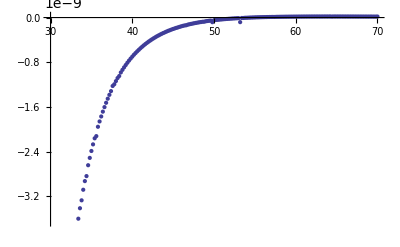

```mathematica
ListPlot[{t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

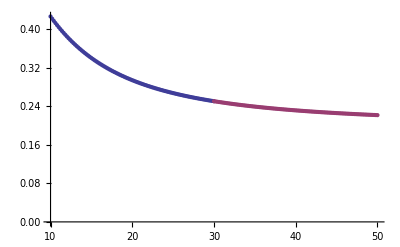

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.25/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.25/I.dat",Join[t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.25/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.25/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```